```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\WF94Fig3\MultiWell\TH\1500_1

## Functions

```mathematica
Clear[TwoAxisListLogandListPlot]
```

```mathematica
TwoAxisListLogandListPlot[f_List,g_List,opts:OptionsPattern[]]:=Module[{p1,p2,fm,fM,gm,gM,oldgtick,newgtick,newg,oldftick,newftick},p1=ListLogPlot[f,Axes->True,Frame->False,PlotRange->All];
p2=ListPlot[g,Axes->True,Frame->False,PlotRange->{All,{0,Max[g⟦All,2⟧]}}];
{fm,fM}=AbsoluteOptions[p1,PlotRange][[1,2,2]];
{gm,gM}=AbsoluteOptions[p2,PlotRange][[1,2,2]];
oldgtick=AbsoluteOptions[p2,Ticks][[1,2,2]];
newgtick=Flatten[{Rescale[First[#1],{gm,gM},{fm,fM}],Rest[#1]},1]&/@oldgtick;
oldftick=AbsoluteOptions[p1,Ticks][[1,2,2]];
newftick=Flatten[{Exp[First[#1]],Rest[#1]},1]&/@oldftick;
newg={#[[1]],Rescale[#[[2]],{gm,gM},{fm,fM}]}&/@g;
Show[ListPlot[newg,Axes->False,Frame->True,FrameTicks->{Automatic,oldftick,Automatic,newgtick},PlotRange->All,PlotStyle-> Black,opts],
ListLogPlot[{f},Axes->False,Frame->{{True,True},{True,True}},FrameTicks->{Automatic,Automatic,Automatic,new},PlotRange->All,PlotStyle-> Blue,opts]]]
```

## Read Data

```mathematica
kineticdata=Import["data.txt","Data"];
```

## Outline

nC4H5 is the initial well. C2H2+C2H3 and C4H4+H are two exit channels.
Thermal instead of Chemical activation.

## Consumed Species: nC4H5 mole fraction: nC4H5; Evib: nC4H5

### configuration

```mathematica
vibname="nC4H5";
concename="nC4H5";
timeEvib=kineticdata⟦All,{1,8}⟧;
timeConcen=kineticdata⟦All,{1,6}⟧;
```

### plot

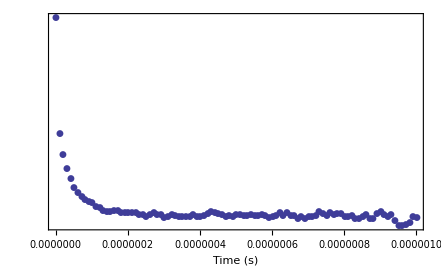

```mathematica
plotframe={{,Style["<Evib> of "<>vibname<>" (cm^-1)",Italic,17]},{Style["Time (s)",Italic,17],}};
ListPlot[timeEvib,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  FrameTicks-> {{None,All},{Automatic, Automatic}},
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotRange-> All,
                  PlotMarkers-> {Automatic}
                    (*PlotLabel->Style["R1→ P1, Θ = 1 atm","Title",Bold,15]*)]
```

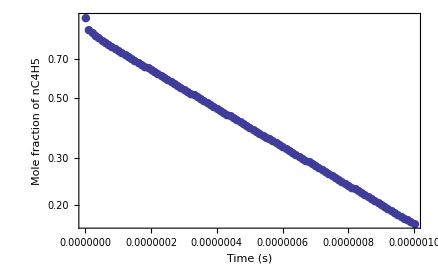

```mathematica
plotframe={{Style["Mole fraction of " <>concename,Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[timeConcen,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Tiny}
                    (*PlotLabel->Style["R1→ P1, Θ = 1 atm","Title",Bold,15]*)]
```

NumberForm::iprf: Formatting specification StyleBox[{∞, "2."}, "MT"] should be a positive integer or a pair of positive integers.

General::stop: Further output of NumberForm will be suppressed during this calculation.

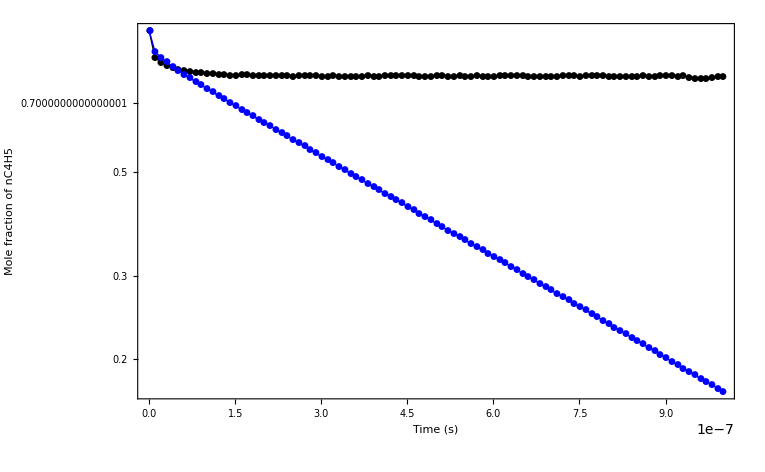

```mathematica
plotframe={{Style["Mole fraction of " <>concename,Italic,17],Style["<Evib> of "<>vibname<>" (cm^-1)",Italic,17]},{Style["Time (s)",Italic,17],}};
TwoAxisListLogandListPlot[timeConcen,timeEvib,FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  PlotMarkers-> {Automatic},
                  Joined-> True,FrameTicksStyle-> 17]
```

### Fit

From above Figure, Evib has been a constant for the last 50 points.
unit of kfit: 1/s
unit of Afit: mole fraction, thus no unit.

```mathematica
startindex=50;
```

```mathematica
timeConcenFit=timeConcen⟦startindex;;⟧
```

{{4.9×10^-7,0.3953},{5.×10^-7,0.389},{5.1×10^-7,0.3821},{5.2×10^-7,0.3759},{5.3×10^-7,0.3701},{5.4×10^-7,0.3645},{5.5×10^-7,0.3582},{5.6×10^-7,0.3525},{5.7×10^-7,0.3469},{5.8×10^-7,0.341},{5.9×10^-7,0.3355},{6.×10^-7,0.3303},{6.1×10^-7,0.3253},{6.2×10^-7,0.32},{6.3×10^-7,0.3146},{6.4×10^-7,0.3096},{6.5×10^-7,0.3041},{6.6×10^-7,0.2993},{6.7×10^-7,0.2943},{6.8×10^-7,0.2897},{6.9×10^-7,0.2848},{7.×10^-7,0.2802},{7.1×10^-7,0.2755},{7.2×10^-7,0.2712},{7.3×10^-7,0.2671},{7.4×10^-7,0.2622},{7.5×10^-7,0.2581},{7.6×10^-7,0.2541},{7.7×10^-7,0.2498},{7.8×10^-7,0.2456},{7.9×10^-7,0.2415},{8.×10^-7,0.2372},{8.1×10^-7,0.2333},{8.2×10^-7,0.2297},{8.3×10^-7,0.226},{8.4×10^-7,0.2222},{8.5×10^-7,0.2185},{8.6×10^-7,0.215},{8.7×10^-7,0.2113},{8.8×10^-7,0.2079},{8.9×10^-7,0.2044},{9.×10^-7,0.2009},{9.1×10^-7,0.1975},{9.2×10^-7,0.1941},{9.3×10^-7,0.1909},{9.4×10^-7,0.1876},{9.5×10^-7,0.1846},{9.6×10^-7,0.1818},{9.7×10^-7,0.1789},{9.8×10^-7,0.176},{9.9×10^-7,0.1731},{1.×10^-6,0.1701}}

```mathematica
{Afit,kfit}=Part[#1,2]&/@FindFit[timeConcenFit,a*Exp[-k*t],{a,k},t]
(*FindFit[timeConcenFit,a*Exp[-k*t],{a,k},t]⟦All,2⟧*)
```

{0.888789,1.65077×10^6}

```mathematica
ScientificForm[Afit*Exp[-kfit*t],3]
```

(8.89×10^-1) ⅇ^((-1.65×10^6) t)

```mathematica
Graphics[{Text[Style["Fit after the "<>ToString[startindex]<>"th point: "<>ToString[ Afit]Exp[-kfit*t],17],{1,1},{0,-2}]}];
```

## All Species: nC4H5,iC4H5, C2H2+C2H3,C4H4+H

### All species

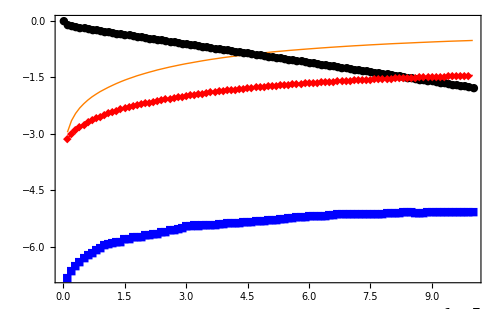

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,6}⟧,kineticdata⟦All,{1,3}⟧,kineticdata⟦All,{1,9}⟧,kineticdata⟦All,{1,12}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Black,Blue,Red,Orange},
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Black:nC4H5,Blue:iC4H5, Red:C2H2+C2H3, Orange:C4H4+H" ]
```

### Produced Species: iC4H5, C2H2+C2H3,C4H4+H

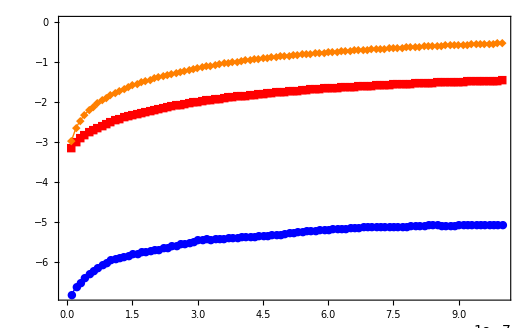

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,3}⟧,kineticdata⟦All,{1,9}⟧,kineticdata⟦All,{1,12}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Blue,Red,Orange},
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Blue:iC4H5, Red:C2H2+C2H3, Orange:C4H4+H" ]
```

### Product (Bimolecular) Channel: C2H2+C2H3, C4H4+H

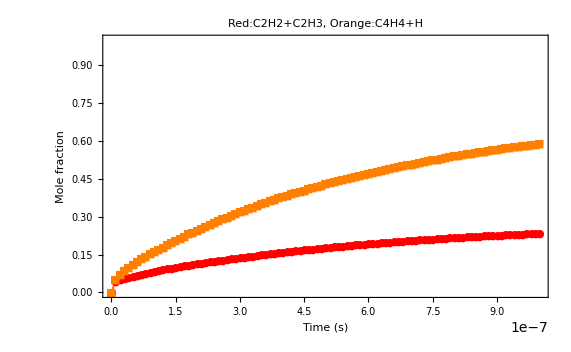

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListPlot[{kineticdata⟦All,{1,9}⟧,kineticdata⟦All,{1,12}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Red,Orange},
                  PlotMarkers-> {Automatic,Tiny},PlotRange-> {All,{0,1}},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Red:C2H2+C2H3, Orange:C4H4+H" ]
```

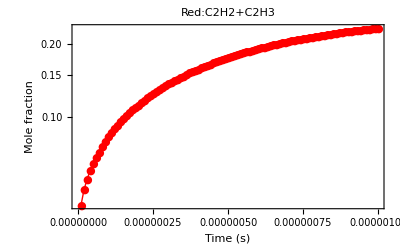

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,9}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Red},
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Red:C2H2+C2H3" ]
```

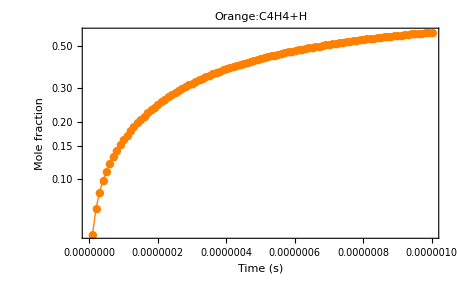

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,12}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Orange},
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Orange:C4H4+H" ]
```

### Product: Mole fraction ratio

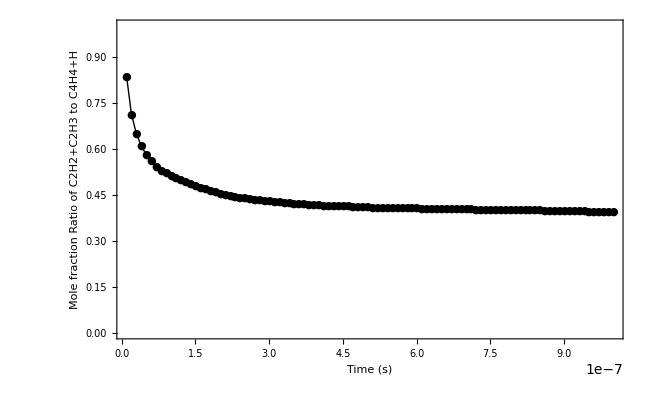

```mathematica
plotframe={{Style["Mole fraction Ratio of C2H2+C2H3 to C4H4+H",Italic,17],},{Style["Time (s)",Italic,17],}};
ListPlot[Table[{kineticdata⟦i,1⟧,kineticdata⟦i,9⟧/kineticdata⟦i,12⟧},{i,2,Length[kineticdata⟦All,1⟧]}],
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Black},
                  PlotMarkers-> {Automatic,Tiny},PlotRange-> {All,{0,1}},Joined-> True,FrameTicksStyle-> 17
                   ]
```

### Unimolecular Channel: nC4H5,iC4H5

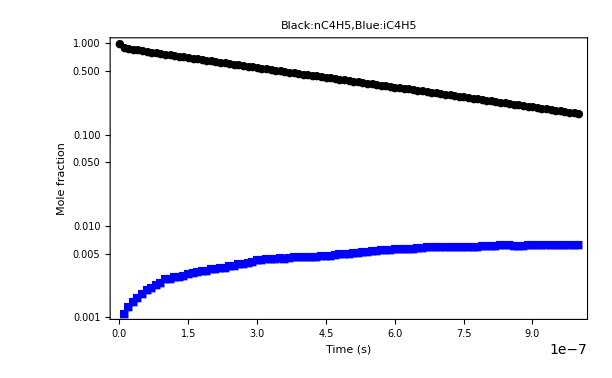

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,6}⟧,kineticdata⟦All,{1,3}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Black,Blue},
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Black:nC4H5,Blue:iC4H5" ]
```

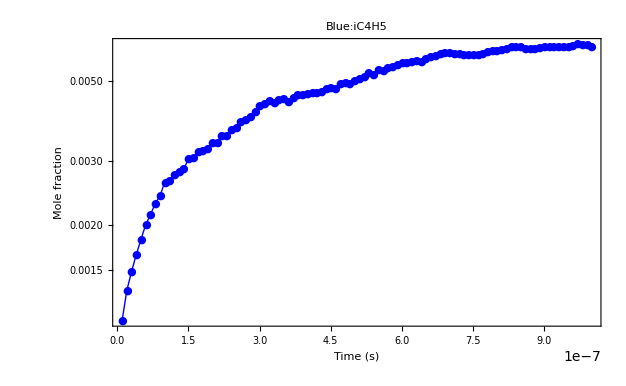

```mathematica
plotframe={{Style["Mole fraction",Italic,17],},{Style["Time (s)",Italic,17],}};
ListLogPlot[{kineticdata⟦All,{1,3}⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,PlotStyle-> {Blue},PlotRange-> All,
                  PlotMarkers-> {Automatic,Tiny},Joined-> True,FrameTicksStyle-> 17,
                  PlotLabel->"Blue:iC4H5" ]
```